## To Do & Notes

不仅仅只对限定的四类Type信息处理。

[Done] 对于exponential的，输出中带有科学计数法的话处理 -> 用一个Interpreter替代ToExpression  Interpreter["Number"]["4.35456e-09"]
4.35456×10^-9

...

## Global Path Configure

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/shenjiaming/Desktop/Junior Courses/Network Project/compareFS_v0.1/10K interest:s

## Read in Data

```mathematica
fileName = "exp-grid-rate-trace-10K.txt";
(*分析grid-topo*)
rawdata = Import[fileName];
data = StringSplit[rawdata,"\n"];
n = Length[data]
data2 = Table[StringSplit[row,"\t"],{row,data}];
head = data2⟦1⟧;
entries = data2⟦2;;n⟧;
head
entries⟦1;;5⟧
```

22129

{Time,Node,FaceId,FaceDescr,Type,Packets,Kilobytes,PacketRaw,KilobytesRaw}

{{0.2,0,256,netDeviceFace://,InInterests,0,0,0,0},{0.2,0,256,netDeviceFace://,OutInterests,8004,0,2001,0},{0.2,0,256,netDeviceFace://,InData,44,45.4609,11,11.3652},{0.2,0,256,netDeviceFace://,OutData,0,0,0,0},{0.2,0,256,netDeviceFace://,InSatisfiedInterests,0,0,0,0}}

## Data Preprocessing

```mathematica
(*0号节点对应consumer*)
consumerEntries = Select[entries,StringMatchQ[#⟦2⟧,"0"] &];
(*找到根据节点id把consumer节点分类，本topo中因为只有一个consumer所以差别不大，但是考虑到后面代码的兼容性，还是加这一行*)
consumer = GatherBy[consumerEntries,#⟦2⟧&];
consumer
```

{{{0.2,0,256,netDeviceFace://,InInterests,0,0,0,0},{0.2,0,256,netDeviceFace://,OutInterests,8004,0,2001,0},{0.2,0,256,netDeviceFace://,InData,44,45.4609,11,11.3652},2560,{19.8,0,258,appFace://,OutTimedOutInterests,0,0,0,0},{19.8,0,-1,all,SatisfiedInterests,119.194,0,24,0},{19.8,0,-1,all,TimedOutInterests,9664.17,0,1922,0}}}
 |  |  |  |

```mathematica
(*找出consumer节点集合中第一个consumer，读出其中Type为一下四类的entries*) 
tmp = Table[Select[consumer⟦1⟧,
StringMatchQ[#⟦5⟧,t]&&!(StringMatchQ[#⟦4⟧, "all"])&],
{t,{"InInterests","InData","OutInterests","OutData"}}];
(*读出符合条件的entires中的times和Kilobytes信息*)
times = Table[Interpreter["Number"][ele⟦1⟧],{ele,tmp⟦1⟧}];
inInterests = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦1⟧}];
inData = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦2⟧}];
outInterests = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦3⟧}];
outData = Table[Interpreter["Number"][ele⟦7⟧],{ele,tmp⟦4⟧}];
(*对多个不同的Type处理*)
(*把time和Kilboytes关联起来，然后把相同times下的list聚集起来*)
n = Length[times];
test = Table[
GatherBy[Table[{times⟦i⟧, t⟦i⟧},{i,1,n}],First],
{t,{inInterests,inData,outInterests,outData}}
];
(*形成时间序列数据*)
(*TimeSeries的好处是方便用ML的技巧拟合模型*)
tsdata= Table[Table[
t⟦1⟧⟦1⟧-> Total[Table[ele⟦2⟧,{ele,t}]],
{t,test⟦i⟧}
],{i,1,4}
];
```

```mathematica
tsdata⟦2⟧
```

{0.2→45.4609,0.4→100.088,0.6→177.104,0.8→229.823,1→244.499,1.2→214.314,1.4→237.269,1.6→237.742,1.8→246.111,2→206.366,2.2→235.66,2.4→237.421,2.6→246.046,2.8→239.498,3→238.189,3.2→233.736,3.4→241.173,3.6→226.113,3.8→239.649,4→242.355,4.2→242.896,4.4→243.006,4.6→247.156,4.8→239.72,5→246.506,5.2→239.59,5.4→246.481,5.6→239.585,5.8→246.48,6→247.858,6.2→215.032,6.4→241.565,6.6→238.602,6.8→246.283,7→239.546,7.2→246.472,7.4→247.857,7.6→239.86,7.8→246.534,8→181.682,8.2→181.098,8.4→193.415,8.6→166.921,8.8→132.665,9→179.592,9.2→143.473,9.4→127.976,9.6→157.971,9.8→147.422,10→141.176,10.2→173.021,10.4→129.741,10.6→125.229,10.8→120.19,11→123.32,11.2→123.945,11.4→119.933,11.6→123.268,11.8→119.798,12→123.241,12.2→119.793,12.4→123.24,12.6→119.785,12.8→123.238,13→123.929,13.2→119.93,13.4→123.267,13.6→119.798,13.8→123.241,14→119.793,14.2→123.24,14.4→123.929,14.6→119.93,14.8→123.267,15→119.798,15.2→119.096,15.4→176.788,15.6→151.178,15.8→125.38,16→124.357,16.2→124.153,16.4→119.975,16.6→123.277,16.8→119.8,17→123.241,17.2→119.793,17.4→123.24,17.6→123.929,17.8→119.93,18→123.267,18.2→119.794,18.4→164.529,18.6→128.051,18.8→124.891,19→120.123,19.2→123.306,19.4→123.942,19.6→119.933,19.8→123.268}

## Visualization

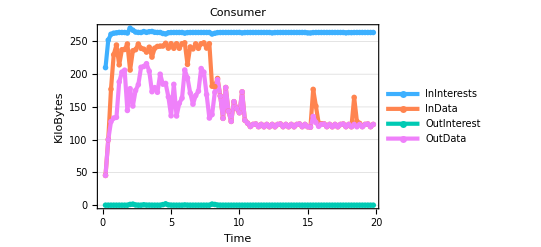

```mathematica
(*四个属性全部画在一起，会发现InInterest和OutInterest完全重合, InData和OutData全部重合，所以看上去只有二根线*)
ListPlot[{
TimeSeries[tsdata⟦1⟧],
TimeSeries[tsdata⟦2⟧],
TimeSeries[tsdata⟦3⟧],
TimeSeries[tsdata⟦4⟧]
},
PlotLabel-> "Consumer",
AxesLabel->{"Time","KiloBytes"},
PlotLegends->{"InInterests","InData","OutInterest","OutData"},
PlotTheme->"Business",
PlotStyle->96,
Joined->True
]
```

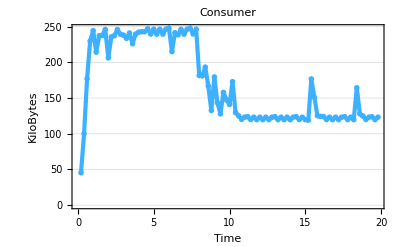

```mathematica
ListPlot[
TimeSeries[tsdata⟦2⟧],
PlotLabel-> "Consumer",
AxesLabel->{"Time","KiloBytes"},
PlotLegends->"InData",
PlotTheme->"Business",
PlotStyle->96,
Joined->True
]
```